```mathematica
(*sampdat=ToExpression[Import["/Users/Tommy/Documents/BU/CH_655_Stat_Mech/New_Final_Project/lattice-reaction-model/lat_react_out201412150457"]][[3;;All]];*)
dat1=importDataOnly["/Users/Tommy/Documents/BU/CH_655_Stat_Mech/New_Final_Project/lattice-reaction-model/output/lat_react_out20141215223217"];
dat2=importDataOnly["/Users/Tommy/Documents/BU/CH_655_Stat_Mech/New_Final_Project/lattice-reaction-model/output/lat_react_out20141215223229"];
dat3=importDataOnly["/Users/Tommy/Documents/BU/CH_655_Stat_Mech/New_Final_Project/lattice-reaction-model/output/lat_react_out20141215223251"]; (*doesn't work?*)
dat4=importDataOnly["/Users/Tommy/Documents/BU/CH_655_Stat_Mech/New_Final_Project/lattice-reaction-model/output/lat_react_out20141215223254"];
dat5=importDataOnly["/Users/Tommy/Documents/BU/CH_655_Stat_Mech/New_Final_Project/lattice-reaction-model/output/lat_react_out20141215223260"];
dat6=importDataOnly["/Users/Tommy/Documents/BU/CH_655_Stat_Mech/New_Final_Project/lattice-reaction-model/output/lat_react_out20141215223279"];
dat7=importDataOnly["/Users/Tommy/Documents/BU/CH_655_Stat_Mech/New_Final_Project/lattice-reaction-model/output/lat_react_out20141215223281"]; (*doesn't work?*)
dat8=importDataOnly["/Users/Tommy/Documents/BU/CH_655_Stat_Mech/New_Final_Project/lattice-reaction-model/output/lat_react_out20141215223287"]; (*doesn't work?*)
dats={dat1,dat2,(*dat3,*)dat4,dat5,dat6(*,dat7,dat8*)};
```

$Aborted

ToExpression::sntxi: Incomplete expression; more input is needed .

Part::take: Cannot take positions 3 through -1 in $Failed.

ToExpression::sntxi: Incomplete expression; more input is needed .

Part::take: Cannot take positions 3 through -1 in $Failed.

ToExpression::sntxi: Incomplete expression; more input is needed .

Part::take: Cannot take positions 3 through -1 in $Failed.

```mathematica
cell[input_]:=Parallelize[DeleteCases[{{White,Rectangle[{0,0}]},input[[1]] {Gray,Rectangle[{0,0}]}, redArrow[input[[2]]], greenArrow[input[[3]]],productCircle[input[[4]]]},0,2]]

cellProd[input_]:=DeleteCases[{{White,Rectangle[{0,0}]},productCircle[input[[4]]]},0,2]

redArrow[pmseed_]:=Abs[pmseed]*{Red,Arrowheads[.2{pmseed-1,1+pmseed}],Arrow[{{0.2,0.1},{0.2,0.9}}]}

greenArrow[pmseed_]:=Abs[pmseed]*{Green,Arrowheads[.2{pmseed-1,1+pmseed}],Arrow[{{0.8,0.1},{0.8,0.9}}]}

productCircle[pmseed_]:=If[
pmseed==1,
{Blue,Circle[{0.5,0.5},0.5]},
If[
pmseed==-1,
{Orange,Circle[{0.5,0.5},0.5]},
0]]


plotASample[sample_]:=
Block[{size},
size=√Length[sample];
Parallelize[GraphicsGrid[Table[Graphics[cell[sample[[size*(i-1)+j]]],PlotRegion->{{0, 0}, {1, 1}}],{i,size},{j,size}],Frame->None]]]


plotASampleProduct[sample_]:=
Block[{size},
size=√Length[sample];
Parallelize[GraphicsGrid[Table[Graphics[cellProd[sample[[size*(i-1)+j]]],PlotRegion->{{0, 0}, {1, 1}}],{i,size},{j,size}],Frame->None]]]


plotMovie[input_]:=
Block[{},
ListAnimate[createMovieFrames[input],AnimationRate->0.8]]


plotMovieandExportAVI[input_,name_]:=
Block[{frames},
frames=Map[Image,createMovieFrames[input]];
Export[ToString[name]<>".avi",frames];
ListAnimate[frames,AnimationRate->0.8]]


createMovieFrames[input_]:=
Block[{size},
size = Length[input];
Parallelize[Table[plotASample[input[[t]]],{t,1,size,1}]]]

exportMovieSWF[input_,name_]:=
Export[ToString[name]<>".swf",createMovieFrames[input]]


exportMovieAVI[input_,name_]:=
Export[ToString[name]<>".avi",ParallelMap[Image,createMovieFrames[input]]]


getProducts[input_]:=(*This function takes a data array and returns an array of the product states*)
Block[{},
input[[All,All,4]]]


plotProductDist[input_]:=(*This function takes a data array and plots the sum of the products over time. This should show if one product is dominant. Uses getProducts. Returns a Plot.*)
Block[{products,samples,productdist},
products=getProducts[input];
samples=Length[products];
productdist=Map[Total,products];
ListLinePlot[productdist]]


plotNumReacted[input_]:=(*This function takes a data array and plots the sum of the Abs of the products. It should show how fast the reactions are taking place. Uses getProducts. Returns a Plot.*)
Block[{products,samples,numReacted},
products=getProducts[input];
samples=Length[products];
numReacted=Map[Total,Abs[products]];
ListLinePlot[numReacted]]

plotsProdExp[input_,name_]:=(*This function takes a data array and plots the sum of the Abs of the products, the sum of the products over time, and the ratio of prod + to total. It should show how fast the reactions are taking place. Uses getProducts. Returns None. Prints 3 Plots*)
Block[{products,samples,numReacted,productDist,ratioPlusToTotal,plotStyle,nrPlot,distPlot,ratioPlot},
products=getProducts[input];
samples=Length[products];
numReacted=ParallelMap[Total,Abs[products]];
productDist=ParallelMap[Total,products];
ratioPlusToTotal=1/2+1/2 productDist/numReacted;
plotStyle={PlotStyle->Directive[18,Black]};
nrPlot=ListLinePlot[numReacted,PlotLabel->"Number Reacted",plotStyle];
distPlot=ListLinePlot[productDist,PlotLabel->"Product Distribution",plotStyle];
ratioPlot=ListLinePlot[ratioPlusToTotal,PlotLabel->"Ratio of Major to Total",plotStyle];
Export[ToString[name]<>"nrPlot.eps",nrPlot];
Export[ToString[name]<>"distPlot.eps",distPlot];
Export[ToString[name]<>"ratioPlot.eps",ratioPlot];
Print[nrPlot];
Print[distPlot];
Print[ratioPlot];]

plotsProd[input_]:=(*This function takes a data array and plots the sum of the Abs of the products, the sum of the products over time, and the ratio of prod + to total. It should show how fast the reactions are taking place. Uses getProducts. Returns None. Prints 3 Plots*)
Block[{products,samples,numReacted,productDist,ratioPlusToTotal,plotStyle,nrPlot,distPlot,ratioPlot},
products=getProducts[input];
samples=Length[products];
numReacted=ParallelMap[Total,Abs[products]];
productDist=ParallelMap[Total,products];
ratioPlusToTotal=1/2+1/2 productDist/numReacted;
plotStyle={PlotStyle->Directive[18,Black]};
nrPlot=ListLinePlot[numReacted,PlotLabel->"Number Reacted",plotStyle];
distPlot=ListLinePlot[productDist,PlotLabel->"Product Distribution",plotStyle];
ratioPlot=ListLinePlot[ratioPlusToTotal,PlotLabel->"Ratio of Major to Total",plotStyle];
Print[nrPlot];
Print[distPlot];
Print[ratioPlot];]

importDataOnly[filepath_]:=(*This function takes a file path to a formatted data file, and returns just the data as an array that can be used as input to plotNumReacted, plotProductDist, among others.*)
ToExpression[Import[filepath]][[3;;All]]
(*This indexing will ignore the header and just give the data. 
The header is the first two rows. The first is a set of strings meant
to be human-readable telling about simulation parameters. The second is the size, number of steps, and sampling interval, meant to be machine-readable (integers).*)
```

```mathematica
testdata=importDataOnly["/Users/Tommy/Documents/BU/CH_655_Stat_Mech/New_Final_Project/lattice-reaction-model/lat_react_out201501122058816"];
plotMovieandExportAVI[testdata,2058816]
```

```mathematica
exportMovieSWF[testdata,"121805760"]
```

121805760.swf

```mathematica
ParallelEvaluate[Off[Parallelize::subpar]]
```

{Null,Null}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

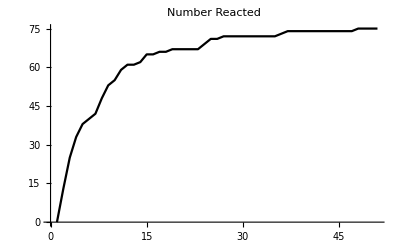

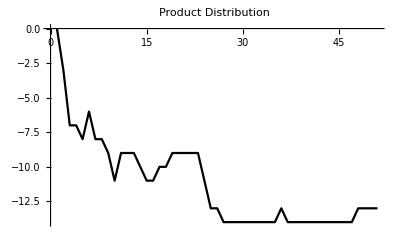

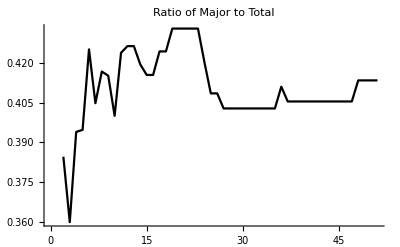

```mathematica
plotsProdExp[testdata,2058816]
```